t_epoch=t_MOT+t_load+n_sequence(n_cold t_attempt+t_cool), where t_attempt=t_OP+t_excite+t_process. The n’s are mean number of entanglement + cooling cycles before the atom is lost and the mean number of entanglement attempts before the atom should be cooled. These values depend on choosing a tolerable survival probability, i.e the probability that the atom is not lost within the events described. 

The epoch, from the above definition t_epoch, is the sequence of loading an atom into the dipole trap, and conducting n_sequence n_cold attempts of entanglement on average before losing the atom. That is, the hierarchy is:
* an epoch is made up of several sequences
* a sequence is made up of several entanglement attempts + one cooling stage

See my OneNote note page “Rate calculations” for further discussion.

```mathematica
(*units*)
ms=10^-3;
μs=10^-6;
ns=10^-9;
(*dependent vars*)
tMOT=500ms;
tLoad =50 ms;
tCool =100 μs;
tOP(*=10 μs*);
tExcite=30 ns;
tProcess=1 μs;
PAttempt;(*survival probability per entanglement attempt*)
PSequence;(*survival probability per sequence of attempts before a cooling stage*)
PEpoch;(*survival probability of the atom during the entire epoch.*)

(*dependent vars*)
nCold(*Floor[Log[PAttempt]/Log[PSequence]+0.5]*);(*number of attempts before atom needs cooling*)
nSequence=1.8(*Floor[Log[PEpoch]/Log[PAttempt]+0.5]*);
nAttempts=nSequence nCold;
tAttempt=tOP μs+tExcite+tProcess;
tEpoch=tMOT+tLoad+nSequence(nCold tAttempt+tCool);
rAttempt =nAttempts/tEpoch; (*the rate of entanglement attempts*)
```

```mathematica
rAttempt//N
```

(1.8 nCold)/(0.55+1.8 (0.0001+nCold (1.03×10^-6+1.×10^-6 tOP)))

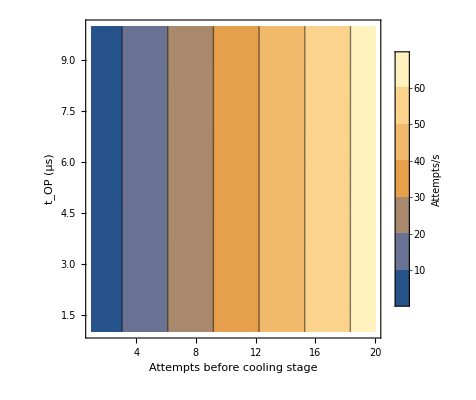

```mathematica
color="SolarColors";
ContourPlot[rAttempt,{nCold,1,20},{tOP,1,10},FrameLabel->{"Attempts before cooling stage","t_OP (μs)"},PlotLegends->BarLegend[Automatic,LegendLabel->"Attempts/s"],LabelStyle->Directive[Black, Medium]]
```

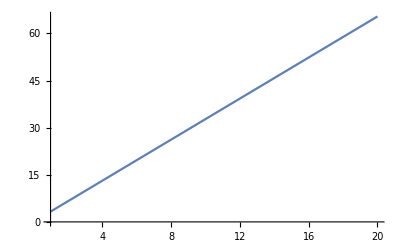

```mathematica
Plot[rAttempt/.tOP->5,{nCold,1,20},PlotStyle->"Scientific",FrameLabel->{"Attempts before cooling stage","t_OP (μs)"},LabelStyle->Directive[Black, Medium]]
```